```mathematica
g=9.81;
l=1;
A=0.5;Ω=20;initpos=π+0.01;w0=Sqrt[g/l];a=-(A*Ω^2/l)
```

-200.

```mathematica
θnor=NDSolve[{θ''[t] +(g/l-(A Ω^2/l) Cos[Ω t])Sin[θ[t]]==0, θ[0]==initpos, θ'[0] == 0}, θ[t], {t,0, 100*π*Sqrt[l/g] }]
```

{{θ[t]→InterpolatingFunction[…][t]}}

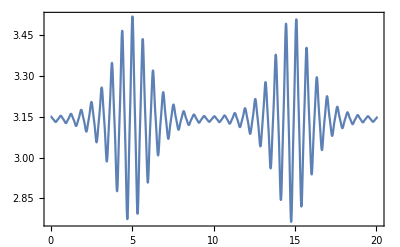

```mathematica
Plot[θ[t]/.θnor,{t,0, 20*π*Sqrt[l/g]},Frame->True,PlotRange->All]
```

```mathematica
f=NDSolve[{θ''[t] +(g/l)Sin[θ[t]]+(A^2*Ω^2/2l^2)Cos[θ[t]]Sin[θ[t]]==0, θ[0]==initpos, θ'[0] == 0}, θ[t], {t,0, 100*π*Sqrt[l/g] }]
```

{{θ[t]→InterpolatingFunction[…][t]}}

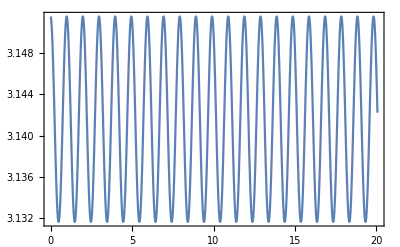

```mathematica
Plot[θ[t]/.f,{t,0, 20*π*Sqrt[l/g]},Frame->True,PlotRange->All]
```

```mathematica
θslow=θ[t]/.f
```

{InterpolatingFunction[…][t]}

```mathematica
Plot[θslow,{t,0, 20*π*Sqrt[l/g]},Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
θfast=-(A/l)Sin[θslow]Cos[Ω*t]
```

{-0.5 Cos[20 t] Sin[InterpolatingFunction[…][t]]}

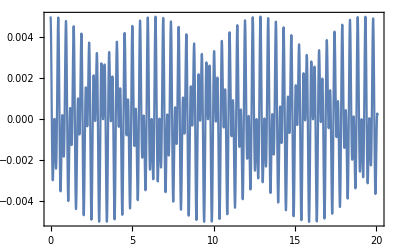

```mathematica
Plot[θfast,{t,0, 20*π*Sqrt[l/g]},Frame->True,PlotRange->All]
```